```mathematica
<<RelationalDatabase`;
```

# TruckFuzzy_SampleFile

## creation date:2015/01/21 update date:2016/07/04

```mathematica
XPosition=1;PItem=2;Fuzzy=3;
```

```mathematica
PT={XPosition,PItem};x=newx;
DB[XPosition]=Union[{x,80,100}];
DB[PItem]={"LE","CE","RI"};
DB[Fuzzy]={.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
```

```mathematica
t=60;
```

```mathematica
rPT[x_]:=Union[{If[0≤x≤t,If[0≤x≤30,{{x,"LE"},{x,"LE"},1},{{x,"LE"},{x,"LE"},(-1/30x+2)}],{{0,"LE"},{0,"LE"},1}]},{If[40≤x≤80,If[40≤x≤60,{{x,"CE"},{x,"CE"},(1/20x-2)},{{x,"CE"},{x,"CE"},(-1/20x+4)}],{{80,"CE"},{80,"CE"},0}]},{If[60≤x≤100,If[60≤x≤80,{{x,"RI"},{x,"RI"},(1/20x-3)},{{x,"RI"},{x,"RI"},1}],{{100,"RI"},{100,"RI"},1}]}];
```

```mathematica
APosition=4;AItem=5;
AT={APosition,AItem};a=newa;
DB[APosition]={-100,a,90,120,190,280};DB[AItem]={"RB","RU","VE","LU","LB"};
```

```mathematica
rAT[a_]:=Union[{If[-100≤a≤10,If[-100≤a≤-45,{{a,"RB"},{a,"RB"},(1/55a+100/55)},{{a,"RB"},{a,"RB"},(-1/55a+10/55)}],{{-100,"RB"},{-100,"RB"},0}]},{If[-10≤a≤90,If[-10≤a≤35,{{a,"RU"},{a,"RU"},(1/45a+10/45)},{{a,"RU"},{a,"RU"},(-1/55a+90/55)}],{{90,"RU"},{90,"RU"},0}]},{If[60≤a≤120,If[60≤a≤90,{{a,"VE"},{a,"VE"},(1/30a-2)},{{a,"VE"},{a,"VE"},(-1/30a+4)}],{{120,"VE"},{120,"VE"},0}]},{If[100≤a≤190,If[100≤a≤155,{{a,"LU"},{a,"LU"},(1/55a-100/55)},{{a,"LU"},{a,"LU"},(-1/55a+190/55)}],{{190,"LU"},{190,"LU"},0}]},{If[170≤a≤280,If[170≤a≤225,{{a,"LB"},{a,"LB"},(1/55a-170/55)},{{a,"LB"},{a,"LB"},(-1/55a+280/55)}],{{280,"LB"},{280,"LB"},1}]}];
```

```mathematica
SItem=6;
DB[SItem]={"NE","ZE","PO"};
IT={PItem,AItem,SItem};
rFR={{{"LE","RB","PO"},{"LE","RB","PO"},1},{{"LE","RU","NE"},{"LE","RU","NE"},1},{{"LE","VE","NE"},{"LE","VE","NE"},1},{{"LE","LU","NE"},{"LE","LU","NE"},1},{{"LE","LB","NE"},{"LE","LB","NE"},1},{{"CE","RB","PO"},{"CE","RB","PO"},1},{{"CE","RU","PO"},{"CE","RU","PO"},1},{{"CE","VE","ZE"},{"CE","VE","ZE"},1},{{"CE","LU","NE"},{"CE","LU","NE"},1},{{"CE","LB","NE"},{"CE","LB","NE"},1},{{"RI","RB","PO"},{"RI","RB","PO"},1},{{"RI","RU","PO"},{"RI","RU","PO"},1},{{"RI","VE","PO"},{"RI","VE","PO"},1},{{"RI","LU","PO"},{"RI","LU","PO"},1},{{"RI","LB","NE"},{"RI","LB","NE"},1}}
```

{{{LE,RB,PO},{LE,RB,PO},1},{{LE,RU,NE},{LE,RU,NE},1},{{LE,VE,NE},{LE,VE,NE},1},{{LE,LU,NE},{LE,LU,NE},1},{{LE,LB,NE},{LE,LB,NE},1},{{CE,RB,PO},{CE,RB,PO},1},{{CE,RU,PO},{CE,RU,PO},1},{{CE,VE,ZE},{CE,VE,ZE},1},{{CE,LU,NE},{CE,LU,NE},1},{{CE,LB,NE},{CE,LB,NE},1},{{RI,RB,PO},{RI,RB,PO},1},{{RI,RU,PO},{RI,RU,PO},1},{{RI,VE,PO},{RI,VE,PO},1},{{RI,LU,PO},{RI,LU,PO},1},{{RI,LB,NE},{RI,LB,NE},1}}

```mathematica
rOut[{XPosition_,X_},{APosition_,P_},{a1_,r1_},{a2_,r2_},{rule_,fr_,out_}]:=Module[{t,g},DB[XPosition]=Union[{X,80,100}];DB[APosition]={-100,P,90,120,190,280};t=FuzzyNaturalJoin[a1,a2,r1[X],r2[P]];g=FuzzyNaturalJoin[Union[a1,a2],rule,t,fr];FuzzyProjection[Union[a1,a2,rule],FuzzyRelComp[FuzzySelection[Union[a1,a2,rule],g,{XPosition}==X],FuzzySelection[Union[a1,a2,rule],g,{APosition}==P]],{out}]]
```

```mathematica
rOut[x_,ϕ_]:=rOut[{XPosition,x},{APosition,ϕ},{PT,rPT},{AT,rAT},{IT,rFR,SItem}]
```

```mathematica
k=rOut[50,100]
```

$Aborted

```mathematica
SPosition=7;s=news;
DB[SPosition]=Range[-30,30.,0.5];
ST={SItem,SPosition};
rST[s_]:=Union[{If[-30≤s≤0,If[-30≤s≤-15,{{"NE",s},{"NE",s},(1/15s+2)},{{"NE",s},{"NE",s},(-1/15s)}],{{"NE",0},{"NE",0},0}]},{If[-5≤s≤5,If[-5≤s≤0,{{"ZE",s},{"ZE",s},(1/5s+1)},{{"ZE",s},{"ZE",s},(-1/5s+1)}],{{"ZE",5},{"ZE",5},0}]},{If[0≤s≤30,If[0≤s≤15,{{"PO",s},{"PO",s},(1/15s)},{{"PO",s},{"PO",s},1}],{{"PO",30.0},{"PO",30.0},1}]}];
```

```mathematica
rs=Union[Flatten[rST[#]&/@Range[-30,30.0,0.5],1]];
```

```mathematica
FuzzySum[c_]:=Sum[c[[i,1]]*Last[c[[i]]],{i,Length[c]}]
```

```mathematica
Expected[c_]:=FuzzySum[c]/Sum[Last[c[[i]]],{i,Length[c]}]
```

```mathematica
Defuzzy[A_,r_,rOut_]:=Module[{rST,rc,a,f},rST=Union[Flatten[r[#]&/@Range[-30,30,0.5],1]];
rc=FuzzyProjection[ST,FuzzyNaturalJoin[ST,{SItem},rs,rOut],{SPosition}];
Expected[rc]]
```

```mathematica
Defuzzy[ST,rST,k]
```

$Aborted

```mathematica
simulateTruck[x0_,y0_,phi0_]:=Module[{x=x0,y=y0,phi=phi0,newPhi,result={}},While[y≤95.,newPhi=phi+Defuzzy[ST,rST,rOut[x,phi]];
AppendTo[result,{x,y,phi}={x+5Cos[newPhi Pi/180],y+ 5Sin[newPhi Pi/180],newPhi}//N];];
result]
```

```mathematica
w=simulateTruck[50,0,100]
```

$Aborted

```mathematica
v=simulateTruck[20,0,-90]
```

{{21.3615,-4.81105,-74.1984},{24.0561,-9.02287,-57.3906},{27.9092,-12.2093,-39.5897},{32.5643,-14.0343,-21.4075},{37.5505,-14.4055,-4.2579},{42.5484,-14.2637,1.62512},{47.5473,-14.3691,-1.20728},{52.5473,-14.3678,0.0141637},{57.5465,-14.2781,1.02786},{62.4818,-13.4764,9.22697},{66.9799,-11.293,25.8924},{70.6186,-7.86369,43.3035},{73.0944,-3.51968,60.3196},{74.1942,1.35785,77.2928},{73.9802,6.35327,92.4532},{72.421,11.1039,108.17},{70.3027,15.6331,115.065},{68.0903,20.117,116.262},{65.7765,24.5494,117.565},{63.4128,28.9553,118.213},{61.322,33.4972,114.718},{59.8477,38.2749,107.15},{59.0678,43.2137,98.9734},{58.5053,48.182,96.4588},{58.2508,53.1755,92.9179},{58.3342,58.1748,89.0445},{58.6217,63.1665,86.7039},{58.8276,68.1623,87.6395},{59.004,73.1592,87.9787},{59.1534,78.157,88.2879},{59.2795,83.1554,88.5538},{59.3865,88.1542,88.7743},{59.4772,93.1534,88.9601},{59.5543,98.1528,89.1165}}

```mathematica
AbsoluteTiming[simulateTruck[20,0,-90]]
```

$Aborted

```mathematica
f[t_]:=Module[{x,w},rPT[x]:=Union[{If[0≤x≤t,If[0≤x≤30,{{x,"LE"},{x,"LE"},1},{{x,"LE"},{x,"LE"},(-1/30x+2)}],{{0,"LE"},{0,"LE"},1}]},{If[40≤x≤80,If[40≤x≤60,{{x,"CE"},{x,"CE"},(1/20x-2)},{{x,"CE"},{x,"CE"},(-1/20x+4)}],{{80,"CE"},{80,"CE"},0}]},{If[60≤x≤100,If[60≤x≤80,{{x,"RI"},{x,"RI"},(1/20x-3)},{{x,"RI"},{x,"RI"},1}],{{100,"RI"},{100,"RI"},1}]}];w=simulateTruck[50,0,100];Sum[(60-w[[i,1]])^2+(100-w[[i,2]])^2,{i,1,Length[w]}]]
```

```mathematica
showTruck[{x_,y_,phi_},{l_,w_}]:=Module[{s=Sin[phi Pi/180]//N,c=Cos[phi Pi/180]//N},Graphics[{Line[Transpose[{x,y}+{{-s w/2,s w/2,s w/2-c l,-1.2 c l,-s w/2-c l,-s w/2},{c w/2,-c w/2,-c w/2-s l,-1.2 s l,c w/2-s l,c w/2}}]],Point[{0,0}],Line[{{0,100},{100,100}}],Line[{{60,100},{60,95}}]},Axes->True,AspectRatio->Automatic,AxesOrigin->{0,0}]]
```

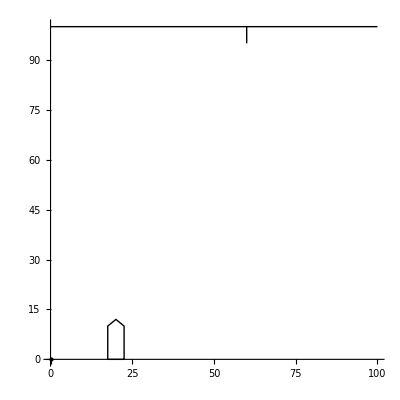

```mathematica
{showTruck[{50,0,100},{10,5}];showTruck[{20,0,-90},{10,5}]}
```

```mathematica
{q=Animate[(showTruck[#,{10,5}]&/@w)[[n]],{n,1,Length[w],1},AnimationRunning->False];p=Animate[(showTruck[#,{10,5}]&/@v)[[n]],{n,1,Length[v],1},AnimationRunning->False]}
```

{}

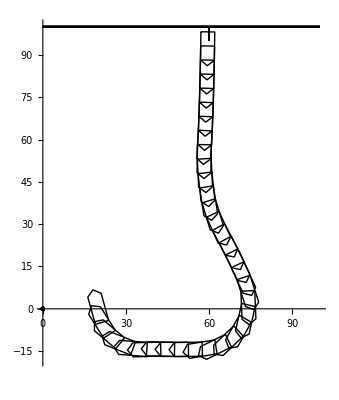

```mathematica
Show[(showTruck[#,{10,5}]&/@v)]
```